```mathematica
Remove["Global`*"]
```

```mathematica
Manipulate[Module[{a=NDSolve[{ m r[t]^2 θ'[t]==l, m r''[t]-l^2/(m r[t]^3)==-k/r[t]^2,r[0]==r0,r'[0]==v,θ[0]==θ0},{θ[t],r[t]},{t,0,100}]},ParametricPlot[{r[t] Cos[θ[t]],r[t] Sin[θ[t]]}/.a,{t,0,T}]],{{r0,1},0.1,20},{{m,1},0.1,5},{{k,2},0.1,5},{{T,5},0,100},{{l,1},0.1,4},{{θ0,0},-Pi,Pi},{{v,0},-2,2}]
```

```mathematica
Manipulate[Module[{a=NDSolve[{ m r[t]^2 θ'[t]==l, m r''[t]-l^2/(m r[t]^3)==-k/r[t]^2,r[0]==r0,r'[0]==v,θ[0]==θ0},θ[t],{t,0,100}]},ParametricPlot[{θ[t],t}/.a,{t,0,T}]],{{r0,1},0.1,20},{{m,1},0.1,5},{{k,2},0.1,5},{{T,5},0,100},{{l,1},0.1,4},{{θ0,0},-Pi,Pi},{{v,0},-2,2}]
```

```mathematica
b=NDSolve[{r[t]^2 θ'[t]==1, r''[t]-1^2/r[t]^3==-1.5/r[t]^2,r[0]==1,r'[0]==0,θ[0]==0},{θ[t],θ'[t],r[t]},{t,0,20}]
```

{{θ[t]→InterpolatingFunction[{{0., 20.}}, <>][t],θ'[t]→InterpolatingFunction[{{0., 20.}}, <>][t],r[t]→InterpolatingFunction[{{0., 20.}}, <>][t]}}

```mathematica
NIntegrate[(1/2 r[t]^2 θ'[t])/.b[[1]],{t,0,10}]
```

5.

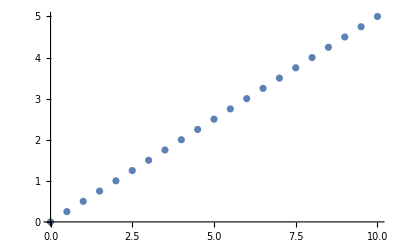
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Table[{Δ,NIntegrate[(1/2 r[t]^2 θ'[t])/.b[[1]],{t,T,T+Δ}]},{Δ,0,10,0.5}]],{T,0,5,1}]
```